b=77.06

m=3.07455

R^2=0.872207

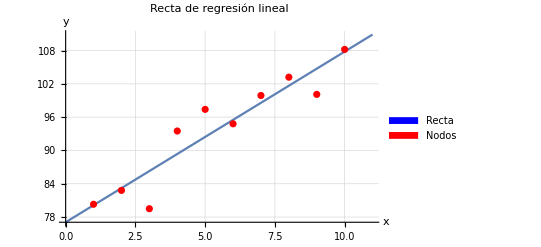

```mathematica
Clear["Global'*"]
x = {1,2,3,4,5,6,7,8,9,10};
y = {80.3,82.8,79.5,93.5,97.4,94.8,99.9,103.2,100.1,108.2};
len=Length[x];
sigmaX = Total[x];
sigmaY = Total[y];
sigmaXY = Sum[x[[i]]*y[[i]],{i,1,len}];
sigmaX2=Sum[x[[i]]*x[[i]],{i,1,len}];
sigmaY2=Sum[y[[i]]*y[[i]],{i,1,len}];
m=(len*sigmaXY-sigmaX*sigmaY)/(len*sigmaX2-(sigmaX)^2);
b=(sigmaY*sigmaX2-sigmaX*sigmaXY)/(len*sigmaX2-(sigmaX)^2);
r=(len*sigmaXY-sigmaX*sigmaY)/Sqrt[(len*sigmaX2-(sigmaX)^2)*(len*sigmaY2-(sigmaY)^2)];
Print["b","=",b];
Print["m","=",m];
Print["R^2","=",r^2];
f[x]:=m*x+b
plot1=Plot[m*x+b,{x,0,11}];
plot2=ListPlot[y,PlotStyle->Red];
Legended[Show[plot1,plot2,PlotLabel->"Recta de regresión lineal",
AxesLabel->{"x","y"},PlotRange->All,GridLines->Automatic],SwatchLegend[{Blue,Red},{"Recta","Nodos"}]]
```